```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SetEnvironment["PATH"->Import["!source ~/.zshrc; echo $PATH","Text"]];
```

```mathematica
toMMA[s_String] := ToExpression[StringReplace[s,{"["->"{", "]" ->"}"}]];
```

```mathematica
plotRow[xs_] := GraphicsRow[ArrayPlot[#, Mesh->True]& /@ xs, 5];
```

```mathematica
ms = ExternalEvaluate["Shell", "cabal run magicsquare -- 8 4 2"]
```

[[[0,0,0,0,1,1,1,1],[0,0,0,0,1,1,1,1],[0,0,1,1,1,0,0,1],[0,1,1,0,0,0,1,1],[1,1,0,0,0,1,1,0],[1,0,0,1,1,1,0,0],[1,1,1,1,0,0,0,0],[1,1,1,1,0,0,0,0]],[[0,0,0,0,1,1,1,1],[0,0,0,1,1,0,1,1],[0,0,1,0,1,1,0,1],[0,1,1,0,0,0,1,1],[1,1,0,0,0,1,1,0],[1,0,0,1,1,1,0,0],[1,1,1,1,0,0,0,0],[1,1,1,1,0,0,0,0]]]

Success[…]

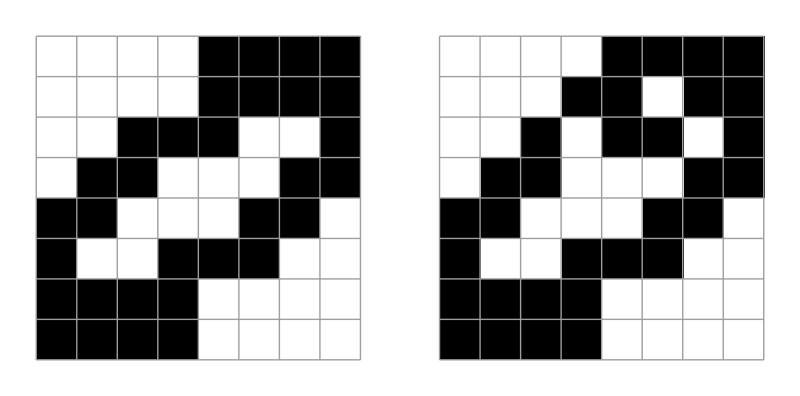

```mathematica
plotRow[toMMA[ms["StandardOutput"]]]
```